```mathematica
Clear["Global`*"]
```

```mathematica
(* g is an increasing function of z. *)
eq1=Collect[Simplify[(1-z)*ggy+z*ggz-g^2/.{ggy->Qdg*g,ggz->(Qcg-Qdg)*g2+Qdg*g}],g2];
eq2=Collect[Simplify[z(1-z)*gy^2+(g-(1-z)*gy)^2-z*g2/.{gy->Qdg}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}]
```

-g^2+g Qdg+(Qcg-Qdg) (g^2+2 g Qdg (-1+z)-Qdg^2 (-1+z))

{(2 g-Qdg) (Qcg-Qdg) Qdg,-2 g+2 g Qcg+Qdg-2 g Qdg-2 Qcg Qdg+2 Qdg^2+2 Qcg Qdg z-2 Qdg^2 z}

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0>0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

True

True

```mathematica
(* Pij and Qij for the simple standing norm. *)
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g≥0,FullSimplify@Reduce[Qcg≥Qdg]] (* If g=0 or 1 then Qcg = Qdg. *)
```

True

```mathematica
(* z=1 implies that g=gz=1. *)
Simplify[Qcg*g^2+Qdg*(g-g^2)+1-2*g]
```

(-1+g)^2

```mathematica
(* Find the cubic numerator of f = πz - πy (given a postive denominator). *)
numdomzy=NumeratorDenominator[Together[r*(g-Qdg)-g]];
polyzy = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzy[[2]]]]*numdomzy[[1]];
{c0,c1,c2,c3}=Simplify[CoefficientList[polyzy,g]];
```

```mathematica
(* Prove that c0 > 0, c3 > 0, and c2 and c3 can't both be positive. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c1<0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c2> 0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c3<0]]
```

True

2 e+r ϵ>1+e r

True

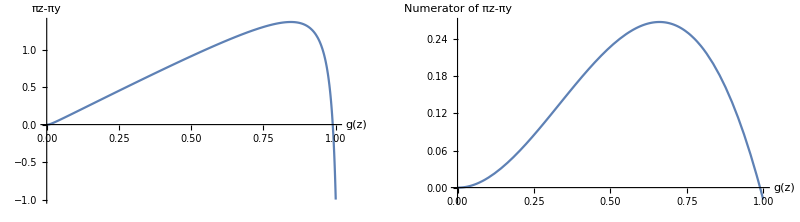

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(g-Qdg)-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πy"}],
Plot[Evaluate[polyzy//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πy"}]}]
```

```mathematica
(* Find the cubic numerator of f = πz - πx (given a postive denominator). *)
numdomzx=NumeratorDenominator[Together[r*(g-Qcg)-g]];
polyzx = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzx[[2]]]]*numdomzx[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx,g]];
```

```mathematica
(* The cubic's coefficients. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1<0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1>0&&a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[(a1>0&&a2<0&&a3>0)]]
```

False

True

True

True

False

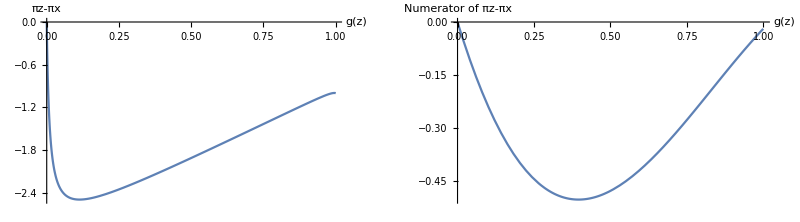

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(g-Qcg)-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πx"}],
Plot[Evaluate[polyzx//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πx"}]}]
```

```mathematica
(* Show that df/dz = -dg/dz and df/dg = -1 at z=0,1 and g=1. *)
Simplify[D[r*(2*g-1-Qcg*g)+1-g/.{g->g[z]},z]/.{g[z]->1}]
Simplify[D[r*(2*g-1-Qcg*g)+1-g,g]/.{g->1}]
```

-g'[z]

-1

```mathematica
(* Prove that pix=piz on the y-axis. *)
eq1=Collect[Simplify[(1-z)*gx+z*gz-g/.{gx->Qcg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gx^2+(g-(1-z)*gx)^2-z*g2/.{gx->Qcg*g+1-g}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}];
```

1+g (-2+Qcg-Qcg z+Qdg z)+(Qcg-Qdg) ((g+(1+g (-1+Qcg)) (-1+z))^2-(1+g (-1+Qcg))^2 (-1+z) z)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1≥ Qcg≥ Qdg≥0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0==0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

3 g+2 Qcg==5||(Qcg≠1&&(g==2/(3-2 Qcg+√(-3+4 Qcg))||g==-2/(-3+2 Qcg+√(-3+4 Qcg))))||Qcg==Qdg

True

```mathematica
Solve[gx==Qcg*g+1-g&&gz==(Qcg-Qdg)*((1-z)*gx^2+z*gz^2)+Qdg*g+1-g&&g==(1-z)*gx+z*gz,{gx,gz}]
```

{}

```mathematica
FullSimplify[(1-gz)*(Qcg*g2+Qdg*(g-g2)+1-g)-gz*((1-Qcg)*g2+(1-Qdg)*(g-g2))]
```

1-gz+g2 Qcg+g (-1+Qdg)-g2 Qdg

```mathematica
FullSimplify[(1-z)*(Qcg*g+1-g)+z*(1-g+Qcg*g2+Qdg*(g-g2))-g]
```

1-2 g+g Qcg+(-g+g2) (Qcg-Qdg) z

```mathematica
FullSimplify[z*gz+(1-z)*gx-z*gz^2-(1-z)*gx^2]
```

gx+gx^2 (-1+z)-gx z-(-1+gz) gz z

```mathematica
(* Lemma A.3.3: On the line y=0, g=gx=gz=1 and thus piz=pix *)
```

```mathematica
FullSimplify[(1-gz)*(Qcg*g2+Qdg*(g-g2))-gz*((1-Qcg)*g2+(1-Qdg)*(g-g2))]
```

g2 (Qcg-Qdg)+g (-gz+Qdg)

```mathematica
FullSimplify[(1-z)*(Qcg*g+1-g)+z*(1-g+Qcg*g2+Qdg*(g-g2))-g]
```

1-2 g+g Qcg+(-g+g2) (Qcg-Qdg) z

```mathematica
FullSimplify[1-g+Qcg*g2+Qdg*(g-g2)-g]
```

```mathematica
FullSimplify[g2 (Qcg-Qdg)+g (-2+Qdg)-g*(Qcg-2)]
```

-(g-g2) (Qcg-Qdg)

```mathematica
FullSimplify[(1-z)*Qcg*g+z*((Qcg-Qdg)*g2+Qdg*g)-g^2]
```

g (-g+Qcg)-(g-g2) (Qcg-Qdg) z

```mathematica
Solve[Qcg-g==0,g]
```

{{g→0},{g→1},{g→1}}

```mathematica
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e1*e&&1≥e1>0&&1>ϵ>0.5>e>0&&1≥g>0&&1≥ Qcg≥ Qdg≥0&&h==0&&1≥z≥0,FullSimplify@Reduce[Qcg>g]]
```

e+g ϵ<e g||g<1

```mathematica
Solve[Qcg==g,g]
```

{{g→0},{g→1},{g→1}}

```mathematica
FullSimplify[(gx-gx2)*Qcg*g-gx2*(1-Qcg)*g]
```

g (-gx2+gx Qcg)

```mathematica
FullSimplify[(gx-gx2)*Qcg*g-gx2*(1-Qcg)*g]
```

```mathematica
FullSimplify[1+e (-1+g)-g ϵ]
```

1+e (-1+g)-g ϵ

```mathematica
Assuming[1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qdg*(1-g)+Qcg*g>g]]
```

False

```mathematica
Assuming[1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>gz>0&&1>g2>0,FullSimplify@Reduce[(Qcg-Qdg)*g2+Qdg*g>g^2]]
```

g2>g^2

```mathematica
FullSimplify[(Qcg-Qdg)*(z*gz^2+(1-z)*Qcg^2)+Qdg*g-g*gz]
```

```mathematica
-g gz+g Qdg+(Qcg-Qdg) (-Qcg^2 (-1+z)+gz^2 z)/.{gz->g}
```

-g^2+g Qdg+(Qcg-Qdg) (-Qcg^2 (-1+z)+g^2 z)

```mathematica
FullSimplify[(Qcg-Qdg)*g2+Qdg*g-g^2]
```

```mathematica
TeXForm[-((-1+g) g (g^2-g2) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))]
```

-\frac{(g-1) g (e-\epsilon )^2 \left(g^2-\text{g2}\right)}{(e (g-1)-g \epsilon )
   (e (g-1)-g \epsilon +1)}

```mathematica
FullSimplify[(1-z)*(Qcg*g)+z*((Qcg-Qdg)*g2+Qdg*g)-g^2]
```

g (-g+Qcg)-(g-g2) (Qcg-Qdg) z

```mathematica
Mslow={{λ,0,0,0,0,0,0,0},{0,λ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
Mslow={{λ,0,0,0,0,0,0,0,0},{0,λ,0,0,0,0,0,0,0},{0,0,λ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}};
Mfast={{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,λ,0,0,0,0,0},{0,0,0,λ,0,0,0,0},{0,0,0,0,λ,0,0,0},{0,0,0,0,0,λ,0,0},{0,0,0,0,0,0,λ,0},{0,0,0,0,0,0,0,λ}};
```

```mathematica
Mslow={{λ,0,0,0,0,0,0,0},{0,λ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
reputations={g->x*gx+(1-x-z)*gy+z*gz,g2->x*gx2+(1-x-z)*gy2+z*gz2};
pix=r*(x+gx*z)-1;
piy=r*(x+gy*z);
piz=r*(x+gz*z)-g/.reputations;
pibar=x*pix+y*piy+z*piz;
fx=(pix-pibar)*x/.reputations;
fz=(piz-pibar)*z/.reputations;
hx=η*(Qcg-gx)*g/.reputations;
hy=η*(Qdg-gy)*g/.reputations;
hz=η*((Qcg-Qdg)*g2+Qdg*g-gz*g)/.reputations;
hx2=η*(gx^2-gx2)*g/.reputations;
hy2=η*(gy^2-gy2)*g/.reputations;
hz2=η*(gz^2-gz2)*g/.reputations;
(*Simplify[Det[FullSimplify[Grad[{fx,fz,hx,hy,hz,hx2,hy2,hz2},{x,z,gx,gy,gz,gx2,gy2,gz2}]/.{z->1-x,gx->1,gy->1,gz->1,gx2->1,gz2->1}]-Mfast]]*)
```

```mathematica
gx=Qcg;
gy=Qdg;
gz=(Qcg-Qdg)*g2/g+Qdg/.{g2->x*gx2+(1-x-z)*gy2+z*gz2};
```

```mathematica
inv=piy-x*pix-y*piy-z*piz/.{z->1-x-y};
```

```mathematica
FullSimplify[Together[inv]]
```

(e^2 (-1+g) ((-1+gx2) x+gy2 y+gz2 (-1+r) (-1+x+y)^3-(gx2 x+gy2 y) (r (-1+x+y)^2-(-2+x+y) (x+y))+g (-1+y+x (3-x-y+r (-1+x+y))))+ϵ (-g x+(-1+r) (-1+x+y)^2 (gx2 x+gy2 y-gz2 (-1+x+y)) ϵ+g (-1+r) (-1+x+y) ((-1+gx2) x+gy2 y+gz2 (-1+x+y)^2-(x+y) (gx2 x+gy2 y)) ϵ+g^2 (-1+x+y+ϵ-y ϵ+(-1+r) x (-1+x+y) ϵ))-e (-1+g) (-x+2 (-1+r) (-1+x+y)^2 (-gx2 x-gy2 y+gz2 (-1+x+y)) ϵ+g (-1+x+y+2 x (2-x-y+r (-1+x+y)) ϵ)))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
eqs=FullSimplify[-(e^2 (-1+g) ((-1+gx2) x+gy2 y+gz2 (-1+r) (-1+x+y)^3-(gx2 x+gy2 y) (r (-1+x+y)^2-(-2+x+y) (x+y))+g (-1+y+x (3-x-y+r (-1+x+y))))+ϵ (-g x+(-1+r) (-1+x+y)^2 (gx2 x+gy2 y-gz2 (-1+x+y)) ϵ+g (-1+r) (-1+x+y) ((-1+gx2) x+gy2 y+gz2 (-1+x+y)^2-(x+y) (gx2 x+gy2 y)) ϵ+g^2 (-1+x+y+ϵ-y ϵ+(-1+r) x (-1+x+y) ϵ))-e (-1+g) (-x+2 (-1+r) (-1+x+y)^2 (-gx2 x-gy2 y+gz2 (-1+x+y)) ϵ+g (-1+x+y+2 x (2-x-y+r (-1+x+y)) ϵ)))]
```

-e^2 (-1+g) ((-1+gx2) x+gy2 y+gz2 (-1+r) (-1+x+y)^3-(gx2 x+gy2 y) (r (-1+x+y)^2-(-2+x+y) (x+y))+g (-1+y+x (3-x-y+r (-1+x+y))))-ϵ (-g x+(-1+r) (-1+x+y)^2 (gx2 x+gy2 y-gz2 (-1+x+y)) ϵ+g (-1+r) (-1+x+y) ((-1+gx2) x+gy2 y+gz2 (-1+x+y)^2-(x+y) (gx2 x+gy2 y)) ϵ+g^2 (-1+x+y+ϵ-y ϵ+(-1+r) x (-1+x+y) ϵ))+e (-1+g) (-x+2 (-1+r) (-1+x+y)^2 (-gx2 x-gy2 y+gz2 (-1+x+y)) ϵ+g (-1+x+y+2 x (2-x-y+r (-1+x+y)) ϵ))

```mathematica
FullSimplify[((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))]
```

(e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ)

```mathematica
Assuming[r>1&&1≥g≥0&&1>ϵ>0.5>e>0,FullSimplify@Reduce[(1+e (-1+g)-g ϵ)<0]]
```

False

```mathematica
FullSimplify[1+e (-1+g)-g ϵ]
```

1+e (-1+g)-g ϵ

```mathematica
Limit[Limit[mysol,y->0],g->1]
```

lim_(g→1) (lim_(y→0) {{x→(0.5 (-1.-(0.0188179 g)/(0.99-0.9702 g)+(1.91178 g)/(0.01+0.9702 g)+(0.0768398 g^2)/(0.99-0.9702 g)-(3.80396 g^2)/(0.01+0.9702 g)+(0.0384199 g y)/(0.99-0.9702 g)-(1.90198 g y)/(0.01+0.9702 g)-(0.0768398 g^2 y)/(0.99-0.9702 g)+(3.80396 g^2 y)/(0.01+0.9702 g)-1. √((1.+(0.0188179 g)/(0.99-0.9702 g)-(1.91178 g)/(0.01+0.9702 g)-(0.0768398 g^2)/(0.99-0.9702 g)+(3.80396 g^2)/(0.01+0.9702 g)-(0.0384199 g y)/(0.99-0.9702 g)+(1.90198 g y)/(0.01+0.9702 g)+(0.0768398 g^2 y)/(0.99-0.9702 g)-(3.80396 g^2 y)/(0.01+0.9702 g))^2-4. (-(0.0384199 g)/(0.99-0.9702 g)+(1.90198 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g)) ((0.019602 g)/(0.99-0.9702 g)+(0.009802 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g)-(0.019602 g y)/(0.99-0.9702 g)-(0.009802 g y)/(0.01+0.9702 g)-(0.0768398 g^2 y)/(0.99-0.9702 g)+(3.80396 g^2 y)/(0.01+0.9702 g)+(0.0384199 g^2 y^2)/(0.99-0.9702 g)-(1.90198 g^2 y^2)/(0.01+0.9702 g)))))/(-(0.0384199 g)/(0.99-0.9702 g)+(1.90198 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g))},{x→(0.5 (-1.-(0.0188179 g)/(0.99-0.9702 g)+(1.91178 g)/(0.01+0.9702 g)+(0.0768398 g^2)/(0.99-0.9702 g)-(3.80396 g^2)/(0.01+0.9702 g)+(0.0384199 g y)/(0.99-0.9702 g)-(1.90198 g y)/(0.01+0.9702 g)-(0.0768398 g^2 y)/(0.99-0.9702 g)+(3.80396 g^2 y)/(0.01+0.9702 g)+√((1.+(0.0188179 g)/(0.99-0.9702 g)-(1.91178 g)/(0.01+0.9702 g)-(0.0768398 g^2)/(0.99-0.9702 g)+(3.80396 g^2)/(0.01+0.9702 g)-(0.0384199 g y)/(0.99-0.9702 g)+(1.90198 g y)/(0.01+0.9702 g)+(0.0768398 g^2 y)/(0.99-0.9702 g)-(3.80396 g^2 y)/(0.01+0.9702 g))^2-4. (-(0.0384199 g)/(0.99-0.9702 g)+(1.90198 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g)) ((0.019602 g)/(0.99-0.9702 g)+(0.009802 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g)-(0.019602 g y)/(0.99-0.9702 g)-(0.009802 g y)/(0.01+0.9702 g)-(0.0768398 g^2 y)/(0.99-0.9702 g)+(3.80396 g^2 y)/(0.01+0.9702 g)+(0.0384199 g^2 y^2)/(0.99-0.9702 g)-(1.90198 g^2 y^2)/(0.01+0.9702 g)))))/(-(0.0384199 g)/(0.99-0.9702 g)+(1.90198 g)/(0.01+0.9702 g)+(0.0384199 g^2)/(0.99-0.9702 g)-(1.90198 g^2)/(0.01+0.9702 g))}})

```mathematica
Solve[3 ((1-x)+x)-x (-1+3 ( (1-x)+x))-(1-x) (-(1-x)- x+3 ( (1-x)+x))==0,x]
```

```mathematica
Simplify[3 ((1-x)+x)-x (-1+3 ( (1-x)+x))-(1-x) (-(1-x)- x+3 ( (1-x)+x))]
```

1

```mathematica
Collect[gz (1-x)^2+x+gx (1-x) x-r x (gx (1-x)+x)+r (gy (1-x)+x)-r (1-x) (gz (1-x)+x),x]
```

```mathematica
FullSimplify[Solve[gz+gy r-gz r+(1+gx-2 gz-gx r-gy r+2 gz r) x+(-gx+gz+gx r-gz r) x^2==0,x]/.{g->0.9}]
```

{{x→-13.6945},{x→0.585604}}

```mathematica
mypoly/.{r->3,gx->Qcg,gy->Qdg,gz->(Qcg-Qdg)*g+Qdg}
```

g (Qcg-Qdg)+4 Qdg-3 (g (Qcg-Qdg)+Qdg)+(1-2 Qcg-3 Qdg+4 (g (Qcg-Qdg)+Qdg)) x+(2 Qcg+g (Qcg-Qdg)+Qdg-3 (g (Qcg-Qdg)+Qdg)) x^2

```mathematica
FullSimplify[Solve[g (Qcg-Qdg)+4 Qdg-3 (g (Qcg-Qdg)+Qdg)+(1-2 Qcg-3 Qdg+4 (g (Qcg-Qdg)+Qdg)) x+(2 Qcg+g (Qcg-Qdg)+Qdg-3 (g (Qcg-Qdg)+Qdg)) x^2==0,x]/.{g->0.9}]
```

{{x→-13.6945},{x→0.585604}}

```mathematica
ϵ=0.9802
e=0.01
```

0.9802

0.01

```mathematica
{{x->(1-2 Qcg+4 g Qcg+Qdg-4 g Qdg-√(1-4 Qcg+8 g Qcg+4 Qcg^2+2 Qdg-8 g Qdg-12 Qcg Qdg+9 Qdg^2))/(4 (-Qcg+g Qcg+Qdg-g Qdg))},{x->(1-2 Qcg+4 g Qcg+Qdg-4 g Qdg+√(1-4 Qcg+8 g Qcg+4 Qcg^2+2 Qdg-8 g Qdg-12 Qcg Qdg+9 Qdg^2))/(4 (-Qcg+g Qcg+Qdg-g Qdg))}}/.{g->0.99}
```

{{x→-0.0240753},{x→-149.012}}

```mathematica
FullSimplify[1-2 Qcg+4 g Qcg+Qdg-4 g Qdg-√(1-4 Qcg+8 g Qcg+4 Qcg^2+2 Qdg-8 g Qdg-12 Qcg Qdg+9 Qdg^2)/.{g->0.99,Qdg->0.98,Qcg->0.99}]
```

0.0113157

```mathematica
{c0,c1,c2}=FullSimplify[CoefficientList[mypoly/.{r->3,gx->Qcg,gy->Qdg,gz->(Qcg-Qdg)*g+Qdg},x]]
```

{Qdg+2 g (-Qcg+Qdg),1+(-2+4 g) Qcg+Qdg-4 g Qdg,-2 (-1+g) (Qcg-Qdg)}

```mathematica
{Qdg+2 g (-Qcg+Qdg),1+(-2+4 g) Qcg+Qdg-4 g Qdg,-2 (-1+g) (Qcg-Qdg)}
```

{Qdg+2 g (-Qcg+Qdg),1+(-2+4 g) Qcg+Qdg-4 g Qdg,-2 (-1+g) (Qcg-Qdg)}

```mathematica
FullSimplify[(-2+2 g+r-2 g r)]
```

```mathematica
Simplify[c/.{r->3}]
```

1-2 Qcg+Qdg

```mathematica
mypoly=Collect[piy-pibar/.{y->0,z->1-x},x]
```

gz+gy r-gz r+(1+gx-2 gz-gx r-gy r+2 gz r) x+(-gx+gz+gx r-gz r) x^2

```mathematica
Solve[-gz (-1+r) (-1+x)^2+x+gx (-1+r) (-1+x) x+gy (r-r x)==0,x]
```

{{x→(-1-gx+2 gz+gx r+gy r-2 gz r-√(-4 (-gx+gz+gx r-gz r) (gz+gy r-gz r)+(1+gx-2 gz-gx r-gy r+2 gz r)^2))/(2 (-gx+gz+gx r-gz r))},{x→(-1-gx+2 gz+gx r+gy r-2 gz r+√(-4 (-gx+gz+gx r-gz r) (gz+gy r-gz r)+(1+gx-2 gz-gx r-gy r+2 gz r)^2))/(2 (-gx+gz+gx r-gz r))}}

```mathematica
FullSimplify[(-1-gx+2 gz+gx r+gy r-2 gz r-√(-4 (-gx+gz+gx r-gz r) (gz+gy r-gz r)+(1+gx-2 gz-gx r-gy r+2 gz r)^2))/(2 (-gx+gz+gx r-gz r))]
```

-1/(2 (gx-gz) (-1+r))(1+gx-2 gz-(gx+gy-2 gz) r+√(4 gz (-1+r)+gx^2 (-1+r)^2+(-1+gy r)^2-2 gx (-1+r) (1+gy r)))

```mathematica
Assuming[r>1&&1≥x≥0&&1≥z≥ 0&&1≥x+z&&1≥gx≥0&&1≥gy≥ 0&&1≥gz≥ 0,FullSimplify@Reduce[piy-pibar<0]]
```

$Aborted

```mathematica
EQ={fx,fz,hx,hy,hz,hx2,hy2,hz2};
J=Grad[EQ,{x,z,gx,gy,gz,gx2,gy2,gz2}]/.{gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1,z->1-x};
Eigenvalues[J]
```

```mathematica
J
```

{{-1+r-(-1+r) (1-x)-(-1+r) x+x (1+r-r (1-x)-r x),x (1+r-r (1-x)-r x),x (r (1-x)+(1-x) x-r (1-x) x),0,-(1-x) x (-1+r (1-x)+x),0,0,0},{(1-x) (1+r-r (1-x)-r x),-1+r-(-1+r) (1-x)-(-1+r) x+(1-x) (1+r-r (1-x)-r x),(1-x) (-x+(1-x) x-r (1-x) x),0,(1-x) (-1+r (1-x)+x-(1-x) (-1+r (1-x)+x)),0,0,0},{0,0,-η+(-1+Qcg) x η,0,(-1+Qcg) (1-x) η,0,0,0},{0,0,(-1+Qdg) x η,-η,(-1+Qdg) (1-x) η,0,0,0},{0,0,(-x+Qdg x) η,0,(-2 (1-x)+Qdg (1-x)-x) η,(Qcg-Qdg) x η,0,(Qcg-Qdg) (1-x) η},{0,0,2 η,0,0,-η,0,0},{0,0,0,2 η,0,0,-η,0},{0,0,0,0,2 η,0,0,-η}}

```mathematica
Det[J-Mslow]
```

0

```mathematica
FullSimplify[Eigenvalues[Grad[{fx,fz},{x,z}]]/.{gx[x,z]->1,gy[x,z]->1,gz[x,z]->1,gx2[x,z]->1,gy2[x,z]->1,gz2[x,z]->1,z->1-x}]
```

{1/2 (1+(-1+x) x ((r+x-r x) gx^(0,1)[x,1-x]+(-1+r) (-1+x) gz^(0,1)[x,1-x]+(-r+(-1+r) x) gx^(1,0)[x,1-x]-(-1+r) (-1+x) gz^(1,0)[x,1-x])-√(1+(-1+x) x ((r (-1+x)-x) gx^(0,1)[x,1-x]+(-1+r+x-r x) gz^(0,1)[x,1-x]+(r+x-r x) gx^(1,0)[x,1-x]+(-1+r) (-1+x) gz^(1,0)[x,1-x]))^2),1/2 (1+(-1+x) x ((r+x-r x) gx^(0,1)[x,1-x]+(-1+r) (-1+x) gz^(0,1)[x,1-x]+(-r+(-1+r) x) gx^(1,0)[x,1-x]-(-1+r) (-1+x) gz^(1,0)[x,1-x])+√(1+(-1+x) x ((r (-1+x)-x) gx^(0,1)[x,1-x]+(-1+r+x-r x) gz^(0,1)[x,1-x]+(r+x-r x) gx^(1,0)[x,1-x]+(-1+r) (-1+x) gz^(1,0)[x,1-x]))^2)}

```mathematica
Assuming[r>1&&1≥x≥0&&gxz∈Reals&&gzz∈Reals&&gxx∈Reals&&gzx∈Reals,FullSimplify@Reduce[1+(-1+x) x ((r+x-r x) gxz+(-1+r) (-1+x) gzz+(-r+(-1+r) x) gxx-(-1+r) (-1+x) gzx)<0]]
```

$Aborted

```mathematica
FullSimplify[Eigenvalues[Grad[{fx,fy},{x,z}]]/.{z->1-x,gx->Qcg*g+1-g,gy->Qdg*g+1-g,gz->Qdg*g+1-g,gz->Qcg*g2+Qdg*(g-g2)+1-g}]/.{g->1,g2->1}
```

{0,-((-x+x ϵ) ζ)/(1-ϵ)}

```mathematica
Simplify[x*gx^2+(1-x)*gz^2-(x*gx+(1-x)*gz)]
```

gz (-1+x)-gz^2 (-1+x)+(-1+gx) gx x

```mathematica
Collect[r*(x+gz*z)-g-piy,z]
```

-g+(-gy r+gz r) z

```mathematica
Eigenvalues[Grad[{hx,hy,hz,hx2,hy2,hz2},{gx,gy,gz,gx2,gy2,gz2}]/.{z->1-x,gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1,η->1}]
```

{-1,-1,-1,-1,-1,(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)}

```mathematica
Solve[(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)==0,x]
```

{{x→1}}

```mathematica
M1=Grad[Evaluate[{fx,fz,hx,hy,hz,hx2,hy2,hz2}/.{y->1-x-z}],{x,z,gx,gy,gz,gx2,gy2,gz2}]/.{z->1-x,gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1,η->1,ζ->1};
```

```mathematica
Simplify[M1/.{gx->Qcg*g+1-g,gy->Qdg*g+1-g,gz->Qdg*g+1-g,gz->Qcg*g2+Qdg*(g-g2)+1-g}]
```

$Aborted

```mathematica
M1slow=Simplify[M1];
```

```mathematica
Collect[Det[M1-Mfast],λ]
```

```mathematica
MatrixForm[M1]
```

```mathematica
Eigensystem[M1]
```

{{0,0,-1,-1,-1,-1,-1,(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)},{{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1/4 (-2+x) (2 x-r x-x^2+r x^2),0,(2-x)/4,-((-2+x) (-e^2-ϵ+2 e ϵ))/(4 (-1+ϵ) ϵ),(2-x)/2,1/2,-(e^2+ϵ-2 e ϵ)/(2 (-1+ϵ) ϵ),1}}}

```mathematica
Grad[M1,{x,z,gx,gy,gz,gx2,gy2,gz2}]
```

```mathematica
Solve[Det[vb-Mfast]==0,λ]
```

```mathematica
Solve[(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)==0,x]
```

{{x→1}}

```mathematica
Solve[-1+r-(-1+r) (1-x)-(-1+r) x==0,x]
```

```mathematica
LinearSolve[M1,ConstantArray[0,8]]
```

```mathematica
MatrixForm[FullSimplify[M1]]
```

(x | x | (r (-1+x)-x) (-1+x) x | 0 | -(-1+r) (-1+x)^2 x | 0 | 0 | 0
1-x | 1-x | -(r (-1+x)-x) (-1+x) x | 0 | (-1+r) (-1+x)^2 x | 0 | 0 | 0
0 | 0 | -1+x | 0 | 1-x | 0 | 0 | 0
0 | 0 | -(x (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ) | -1 | ((-1+x) (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ) | 0 | 0 | 0
0 | 0 | 2 x | 0 | 1-2 x | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | -1)

```mathematica
LinearSolve[M1,ConstantArray[0,8]]
```

{0,0,0,0,0,0,0,0}

```mathematica
eqs=FullSimplify[M1.{x1,-x1,0,0,0,0,0,0}];
MatrixForm[eqs]
```

(0
0
0
0
0
0
0
0)

```mathematica
Solve[((-1+x) (-1+r ))/(-r-x+r x)==0,x]
```

{{x→1}}

```mathematica
Solve[eqs[[1]]==0&&eqs[[3]]==0&&eqs[[4]]==0&&eqs[[5]]==0,{x2,x3,x4,x5}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x3→0,x4→0,x5→0}}

```mathematica
Solve[-1+r-(-1+r) (1-x)-(-1+r) x+x (r (1-x)+(1-x) x-r (1-x) x) x3-(1-x) x (-1+r (1-x)+x) x5==0,{x3}]
```

{{x3→((-1+x) (-x5+r x5))/(-r-x+r x)}}

```mathematica
LinearSolve[M1,ConstantArray[0,8]]
```

{0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[M1]
MatrixForm[FullSimplify[M1/.{x->(1-e)/(ϵ*r)}]]
```

{{0,0,(r (-1+x)-x) (-1+x) x,0,-(-1+r) (-1+x)^2 x,0,0,0},{0,0,0,0,0,0,0,0},{0,0,-1+x,0,1-x,0,0,0},{0,0,-(x (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ),-1,((-1+x) (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ),0,0,0},{0,0,2 x,0,1-2 x,0,0,0},{0,0,2,0,0,-1,0,0},{0,0,0,2,0,0,-1,0},{0,0,0,0,2,0,0,-1}}

(0 | 0 | -((-1+e) (-1+e+r ϵ) ((-1+e) (-1+r)+r^2 ϵ))/(r^3 ϵ^3) | 0 | ((-1+e) (-1+r) (-1+e+r ϵ)^2)/(r^3 ϵ^3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(-1+e+r ϵ)/(r ϵ) | 0 | 1+(-1+e)/(r ϵ) | 0 | 0 | 0
0 | 0 | ((-1+e) (e^2+ϵ-2 e ϵ))/(r (-1+ϵ) ϵ^2) | -1 | -((e^2+ϵ-2 e ϵ) (-1+e+r ϵ))/(r (-1+ϵ) ϵ^2) | 0 | 0 | 0
0 | 0 | (2-2 e)/(r ϵ) | 0 | 1+(2 (-1+e))/(r ϵ) | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | -1)

```mathematica
vb=FullSimplify[M1/.{x->(1-e)/(ϵ*r)}]
```

{{0,0,-((-1+e) (-1+e+r ϵ) ((-1+e) (-1+r)+r^2 ϵ))/(r^3 ϵ^3),0,((-1+e) (-1+r) (-1+e+r ϵ)^2)/(r^3 ϵ^3),0,0,0},{0,0,0,0,0,0,0,0},{0,0,-(-1+e+r ϵ)/(r ϵ),0,1+(-1+e)/(r ϵ),0,0,0},{0,0,((-1+e) (e^2+ϵ-2 e ϵ))/(r (-1+ϵ) ϵ^2),-1,-((e^2+ϵ-2 e ϵ) (-1+e+r ϵ))/(r (-1+ϵ) ϵ^2),0,0,0},{0,0,(2-2 e)/(r ϵ),0,1+(2 (-1+e))/(r ϵ),0,0,0},{0,0,2,0,0,-1,0,0},{0,0,0,2,0,0,-1,0},{0,0,0,0,2,0,0,-1}}

```mathematica
Solve[(1-e) (1-x)+e (1-x)-((1-e) (-(1-e) (1-x)+(1-x) (1-ϵ)))/(1-ϵ)-(e (-e (1-x)+(1-x) ϵ))/ϵ==0,x]
```

{{x→1}}

```mathematica
Eigenvalues[M1]
```

{0,0,-1,-1,-1,-1,-1,(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)}

```mathematica
Solve[(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)==0]
```

{{x→1}}

```mathematica
vc=FullSimplify[vb.{a,b,1,1,1,2,2,2}]
```

{-((-1+e) (-1+e+r ϵ))/(r^2 ϵ^2),0,0,-(e-ϵ)^2/((-1+ϵ) ϵ),1,0,0,0}

```mathematica
vc/.{x->1/2}
```

{1/4 (1/2-r/2)+1/2 (1/4+r/4),0,0,-(2 (1-e) (1/2 (-1+e)+(1-ϵ)/2))/(1-ϵ)-(2 e (-e/2+ϵ/2))/ϵ,1,0,0,0}

```mathematica
Solve[vc[[1]]==0&&vc[[2]]==0&&vc[[3]]==0&&vc[[4]]==0&&vc[[5]]==0,{a,b}]
```

{}

```mathematica
vb/.{r->3,ϵ->0.9802,e->0.01}
```

{{0,0,0.519596,0,-0.296274,0,0,0},{0,0,0,0,0,0,0,0},{0,0,-0.663334,0,0.663334,0,0,0},{0,0,16.665,-1,32.8351,0,0,0},{0,0,0.673332,0,0.326668,0,0,0},{0,0,2,0,0,-1,0,0},{0,0,0,2,0,0,-1,0},{0,0,0,0,2,0,0,-1}}

```mathematica
Eigenvalues[M1]
```

```mathematica
LinearSolve[vb,ConstantArray[0,8]]
```

{0,0,0,0,0,0,0,0}

```mathematica
Simplify[(-ϵ+x ϵ+ϵ^2-x ϵ^2)/((-1+ϵ) ϵ)]
```

1-x

```mathematica
MatrixForm[M1.{x,z,gx,gy,gz,gx2,gy2,gz2}]
```

(-gz (1-x) x (-1+r (1-x)+x)+x (-1+r-(-1+r) (1-x)-(-1+r) x)+gx x (r (1-x)+(1-x) x-r (1-x) x)
0
gz ((1-e) (1-x)+e (1-x))+gx (-1+(1-e) x+e x)
-gy+gz ((1-e) (1-x)+e (1-x)-((1-e) (-(1-e) (1-x)+(1-x) (1-ϵ)))/(1-ϵ)-(e (-e (1-x)+(1-x) ϵ))/ϵ)+gx ((1-e) x+e x-((1-e) (-(1-e) x+x (1-ϵ)))/(1-ϵ)-(e (-e x+x ϵ))/ϵ)
gz ((1-e) (1-x)+e (1-x)-x)+gx (x+(1-e) x+e x)
2 gx-gx2
2 gy-gy2
2 gz-gz2)

```mathematica
M2=Grad[M1.{x,z,gx,gy,gz,gx2,gy2,gz2},{x,z,gx,gy,gz,gx2,gy2,gz2}];
```

```mathematica
Solve[Det[vb-Mslow]==0,λ]
```

{{λ→0},{λ→0}}

```mathematica
FullSimplify[Eigenvalues[Grad[{fx,fz,hx,hy,hz,hx2,hy2,hz2},{x,z,gx,gy,gz,gx2,gy2,gz2}]]/.{z->1-x,ζ->1,gx->1,gy->1,gz->1}]
```

$Aborted

```mathematica
F=Simplify[Grad[{fx,fy,fz,hx,hy,hz,hx2,hy2,hz2},{x,y,z,gx,gy,gz,gx2,gy2,gz2}]/.{y->0,z->1-x,ζ->1,η->1,g->1,gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1}];
```

```mathematica
Solve[Det[F-Mslow]==0,λ]
```

{{λ→0},{λ→0},{λ→1}}

```mathematica
MatrixForm[Grad[{x,y^2},{x,y}]]
```

(1 | 0
0 | 2 y)

```mathematica
coeffs=CoefficientList[Det[F-Mslow],λ]
```

{1,1,((-gz^2+gz2) 6 (e^2 gx-2 e^3 gx+e^4 gx-2 e^2 gz+2 e^3 gz-2 e^2 gx gz+6 e^3 gx gz-4 e^4 gx gz+4 e^2 gz^2-5 e^3 gz^2+635+gx^5 x^4 ϵ^4+8 gx^3 gz x^4 ϵ^4-4 gx^4 gz x^4 ϵ^4-12 gx^2 gz^2 x^4 ϵ^4+6 gx^3 gz^2 x^4 ϵ^4+8 gx gz^3 x^4 ϵ^4-4 gx^2 gz^3 x^4 ϵ^4-2 gz^4 x^4 ϵ^4+gx gz^4 x^4 ϵ^4))/((-e+e gz+e gx x-e gz x-gz ϵ-gx x ϵ+gz x ϵ)^2 (1-e+e gz+e gx x-e gz x-gz ϵ-gx x ϵ+gz x ϵ)^2 (e+e gz (-1+x)-e gx x+(gz+gx x-gz x) ϵ) (-1+e+e gz (-1+x)-e gx x+gx x ϵ+gz (ϵ-x ϵ)))+4+((1)^3 2 (-1+2+1))/((1)^2 (1)^2)}
 |  |  |  |

```mathematica
Solve[coeffs[[3]]==0,x]
```

$Aborted

```mathematica
Simplify[coeffs/.{gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1}]
```

{0,1-x,-1+x}

```mathematica
F-Mslow
```

{{x-λ,x,(r (-1+x)-x) (-1+x) x,0,-(-1+r) (-1+x)^2 x,0,0,0},{1-x,1-x-λ,-(r (-1+x)-x) (-1+x) x,0,(-1+r) (-1+x)^2 x,0,0,0},{0,0,-1+x,0,1-x,0,0,0},{0,0,-(x (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ),-1,((-1+x) (e^2+ϵ-2 e ϵ))/((-1+ϵ) ϵ),0,0,0},{0,0,2 x,0,1-2 x,0,0,0},{0,0,2,0,0,-1,0,0},{0,0,0,2,0,0,-1,0},{0,0,0,0,2,0,0,-1}}

```mathematica
FullSimplify[M1]
```

$Aborted

```mathematica
Simplify[1/4 (2 ζ+gx ζ+gz ζ-gx r ζ+2 gy r ζ-gz r ζ)/.{ζ->1}]
```

1/4 (2+gx+gz-gx r+2 gy r-gz r)

```mathematica
pix=r*(x+gx*z)-1;
piy=r*(x+gy*z);
piz=r*(x+gz*z)-g;
fx=(pix-pibar)*x;
FullSimplify[fx]
```

```mathematica
D[(-1+x+gx r z-(gx-gy) (-1+r) x z+(-1+r) z (gy (-1+z)-gz z)),x]
```

1-(gx-gy) (-1+r) z

```mathematica
Solve[1+r (-1+x)==0,x]
```

{{x→(-1+r)/r}}

```mathematica
Solve[(e^2 (-1+x)-2 e (-1+x) ϵ+(x-ϵ) ϵ)/((-1+ϵ) ϵ)==0/.{ϵ->0.9802,e->0.01},x]
```

{{x→0.979798}}

```mathematica
Solve[1+r (-1+gy+x-gy x)==0,x]/.{r->3,gy->0}
```

{{x→2/3}}

```mathematica
1+r (-1+gy+x-gy x)/.{r->3,gy->1}
```

1

```mathematica
Solve[-(-x+x ϵ)/(1-ϵ)==0,x]
```

{{x→0}}

```mathematica
Qdg/.{g->1}
```

1

```mathematica
px=r*(x+gx[x,z]*z)-1;
py=r*(x+gy[x,z]*z);
pz=r*(x+gz[x,z]*z)-x*gx[x,z]-(1-x-z)*gy[x,z]-z*gz[x,z];
pbar=x*px+(1-x-z)*py+z*pz;
fx=(px-pbar)*x;
fz=(pz-pbar)*z;
```

```mathematica
FullSimplify[Eigenvalues[Grad[{fx,fz},{x,z}]]/.{z->1/2,x->1/2,gx[x,z]->1,gy[x,z]->1,gz[x,z]->1}]
```

{1/16 (8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2]-√((-8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2])^2)),1/16 (8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2]+√((-8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2])^2))}

```mathematica
Solve[1/2 (-2+3 (1-x)+3 x+√((1-x)^2+2 (1-x) x+x^2))==0,x]
```

```mathematica
FullSimplify[1/16 (8-(1+r) Derivative[0,1][gx][1/2,1/2]+(-1+r) Derivative[0,1][gz][1/2,1/2]+(1+r) Derivative[1,0][gx][1/2,1/2]+Derivative[1,0][gz][1/2,1/2]-r Derivative[1,0][gz][1/2,1/2]-√((-8-(1+r) Derivative[0,1][gx][1/2,1/2]+(-1+r) Derivative[0,1][gz][1/2,1/2]+(1+r) Derivative[1,0][gx][1/2,1/2]+Derivative[1,0][gz][1/2,1/2]-r Derivative[1,0][gz][1/2,1/2])^2))]
```

1/16 (8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2]-√((-8-(1+r) gx^(0,1)[1/2,1/2]+(-1+r) gz^(0,1)[1/2,1/2]+(1+r) gx^(1,0)[1/2,1/2]+gz^(1,0)[1/2,1/2]-r gz^(1,0)[1/2,1/2])^2))

```mathematica
Collect[CharacteristicPolynomial[Grad[{fx,fz},{x,z}]/.{z->1/2,x->1/2,gx[x,z]->1,gy[x,z]->1,gz[x,z]->1},λ],λ]
```

λ^2-1/8 gx^(0,1)[1/2,1/2]-1/8 r gx^(0,1)[1/2,1/2]-1/8 gz^(0,1)[1/2,1/2]+1/8 r gz^(0,1)[1/2,1/2]+1/8 gx^(1,0)[1/2,1/2]+1/8 r gx^(1,0)[1/2,1/2]+1/8 gz^(1,0)[1/2,1/2]-1/8 r gz^(1,0)[1/2,1/2]+λ (-1+1/8 gx^(0,1)[1/2,1/2]+1/8 r gx^(0,1)[1/2,1/2]+1/8 gz^(0,1)[1/2,1/2]-1/8 r gz^(0,1)[1/2,1/2]-1/8 gx^(1,0)[1/2,1/2]-1/8 r gx^(1,0)[1/2,1/2]-1/8 gz^(1,0)[1/2,1/2]+1/8 r gz^(1,0)[1/2,1/2])

```mathematica
Grad[{fx,fz},{x,z}]/.{z->1/2,x->1/2,gx[x,z]->1,gy[x,z]->1,gz[x,z]->1}
```

{{1/2 (1+1/2 r (1+1/2 gx^(1,0)[1/2,1/2])+1/2 (1/2 gx^(1,0)[1/2,1/2]-r (1+1/2 gz^(1,0)[1/2,1/2])+1/2 gz^(1,0)[1/2,1/2])),1/2 (1+1/2 r (1+1/2 gx^(0,1)[1/2,1/2])+1/2 (1/2 gx^(0,1)[1/2,1/2]-r (1+1/2 gz^(0,1)[1/2,1/2])+1/2 gz^(0,1)[1/2,1/2]))},{1/2 (1-1/2 r (1+1/2 gx^(1,0)[1/2,1/2])-1/2 gx^(1,0)[1/2,1/2]+r (1+1/2 gz^(1,0)[1/2,1/2])+1/2 (1/2 gx^(1,0)[1/2,1/2]-r (1+1/2 gz^(1,0)[1/2,1/2])+1/2 gz^(1,0)[1/2,1/2])-1/2 gz^(1,0)[1/2,1/2]),1/2 (1-1/2 r (1+1/2 gx^(0,1)[1/2,1/2])-1/2 gx^(0,1)[1/2,1/2]+r (1+1/2 gz^(0,1)[1/2,1/2])+1/2 (1/2 gx^(0,1)[1/2,1/2]-r (1+1/2 gz^(0,1)[1/2,1/2])+1/2 gz^(0,1)[1/2,1/2])-1/2 gz^(0,1)[1/2,1/2])}}

```mathematica
FullSimplify[-1/8 Derivative[0,1][gx][1/2,1/2]-1/8 r Derivative[0,1][gx][1/2,1/2]+1/8 λ Derivative[0,1][gx][1/2,1/2]+1/8 r λ Derivative[0,1][gx][1/2,1/2]-1/8 Derivative[0,1][gz][1/2,1/2]+1/8 r Derivative[0,1][gz][1/2,1/2]+1/8 λ Derivative[0,1][gz][1/2,1/2]-1/8 r λ Derivative[0,1][gz][1/2,1/2]+1/8 Derivative[1,0][gx][1/2,1/2]+1/8 r Derivative[1,0][gx][1/2,1/2]-1/8 λ Derivative[1,0][gx][1/2,1/2]-1/8 r λ Derivative[1,0][gx][1/2,1/2]+1/8 Derivative[1,0][gz][1/2,1/2]-1/8 r Derivative[1,0][gz][1/2,1/2]-1/8 λ Derivative[1,0][gz][1/2,1/2]+1/8 r λ Derivative[1,0][gz][1/2,1/2]]
```

1/8 (-1+λ) ((1+r) gx^(0,1)[1/2,1/2]-(-1+r) gz^(0,1)[1/2,1/2]-(1+r) gx^(1,0)[1/2,1/2]+(-1+r) gz^(1,0)[1/2,1/2])